342837.

Sequence[]

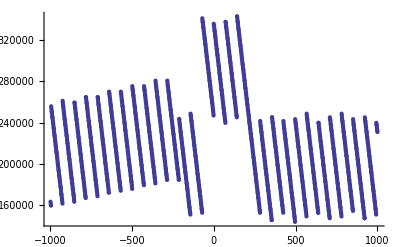

```mathematica
sumofoddharmonics[x_]:=1000*N[1/3-1/2 PolyGamma[5/2]+1/2 PolyGamma[1/2+x]];
bananasrun[initialnumber_,runat_]:=Floor[N[1000runat-(2runat-1)(1000-(sumofoddharmonics[initialnumber]-sumofoddharmonics[runat]))]];

bananasrecurse[init_,recurse_] := If[sumofoddharmonics[init]-sumofoddharmonics[recurse]<1000,bananasrun[init,recurse],bananasrecurse[init,recurse+1]]

bananas[init_] := bananasrecurse[init,1];

efficiency[init_, recurse_]:=Block[{$IterationLimit=1000000000},N[(bananasrecurse[init,recurse]-1000)/(1000init),30]]

l1 = {#,10^18(100*efficiency[10000000000000000+#,1353352832366130]-13.533528323661)}&/@Array[(#-1000)&,2000];
Max[l1]
Pick[l1,342837]
ListPlot[l1]
```

```mathematica
(*
1e1-3.99%
1e2-12.539%
1e3-13.4335%
1e4-13.52352%
1e5-13.532528%
1e6-13.5334283%
1e7-13.53351832%
1e8-13.533527323%
1e9-13.5335282236%
1e10-13.53352831366%
1e11-13.533528322728%
1e12-13.5335283235180%
1e13-13.53352832364689%
1e14-13.533528323659770%
1e15-13.5335283236610568%
1e16-13.53352832366133528%***
1e17-13.533528323661224983%
1e18-13.5335283236611931160%
1e19-13.53352832366125513752%
1e20-13.533528323661221592087%
1e21-13.5335283236611901357079%
*)
```